## № 1

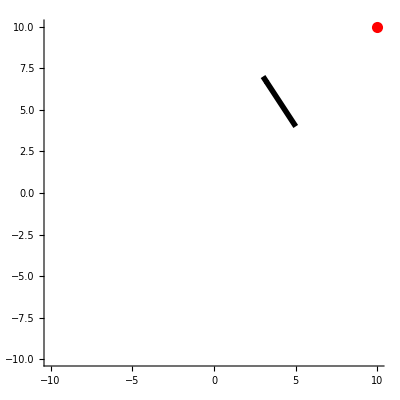

```mathematica
P[n_]:=Table[{Random[Integer,{-10,10}],Random[Integer,{-10,10}]},{n}]
P12=P[2];
P3=P[1][[1]];
Graphics[{Thickness[0.01],Arrow[P12],Red,PointSize[0.02],Point[P3]},PlotRange->{{-10,10},{-10,10}},Axes->True]
```

```mathematica
PointLocation[{P1_,P2_},P3_]:=Block[{d},d=Det[{P2-P1,P3-P1}];If[d!=0,If[d>0, Return["Точка лежит слева от стрелки"],Return["Точка лежит справа от стрелки"]],Return["Точка лежит на прямой"]]]
```

```mathematica
PointLocation[P12,P3]
```

Точка лежит справа от стрелки

## № 2

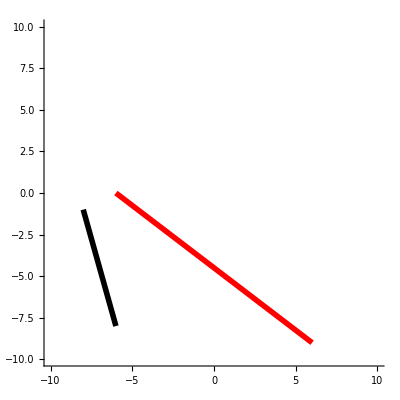

```mathematica
P[n_]:=Table[{Random[Integer,{-10,10}],Random[Integer,{-10,10}]},{n}]
P12=P[2];
P34=P[2];
Graphics[{Thickness[0.01],Line[P12],Red,Thickness[0.01],Line[P34]},PlotRange->{{-10,10},{-10,10}},Axes->True]
```

```mathematica
IsIntersection[{P1_,P2_},{P3_,P4_}]:=Block[{d1,d2,d3,d4,sp1,sp2,sp3,sp4},
d1=Det[{P2-P3,P4-P3}];d2=Det[{P1-P3,P4-P3}]; d3=Det[{P4-P1,P2-P1}];d4=Det[{P3-P1,P2-P1}];
sp1=Dot[P3-P1,P4-P1];sp2=Dot[P3-P2,P4-P2];sp3=Dot[P3-P1,P3-P2];sp4=Dot[P4-P1,P4-P2];
If[d1== d2== d3==d4== 0, 
If[sp1≤0||sp2≤ 0||sp3≤0||sp4≤0,Return[True],Return[False]],
If[d1 d2<0 && d3 d4<0,Return[True],Return[False]]]]
```

```mathematica
IsIntersection[P12,P34]
```

False

## № 3

{{7,-7},{-10,-2},{-8,7},{8,2},{7,-7}}

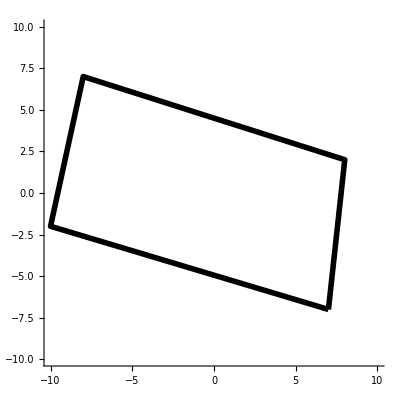

```mathematica
n=Random[Integer,{4,4}];
P[n_]:=Table[{Random[Integer,{-10,10}],Random[Integer,{-10,10}]},{n}]
polinom=P[n]; 
AppendTo[polinom,polinom[[1]]];polinom
Graphics[{Thickness[0.01],Line[polinom]},PlotRange->{{-10,10},{-10,10}},Axes->True]
```

```mathematica
simplify=False;
Do[Do[simplify=IsIntersection[{polinom⟦i⟧,polinom⟦i+1⟧},{polinom⟦j⟧,polinom⟦j+1⟧}];If[simplify==True,Break[],Continue[]],{j,i+2,n}];If[simplify==True,Break[],Continue[]],{i,1,n}];
```

```mathematica
If[simplify== True,"Многоугольник не простой","Многоугольник простой"]
```

Многоугольник простой

## № 4

```mathematica
count=0;
If[simplify==True,count++,
temp=PointLocation[{polinom⟦1⟧,polinom⟦2⟧},polinom⟦3⟧];
For[i=2,i≤n,i++,
If[n>i≥2,convex=PointLocation[{polinom⟦i⟧,polinom⟦i+1⟧},polinom⟦i+2⟧],];
If[i==n,convex=PointLocation[{polinom⟦i⟧,polinom⟦i+1⟧},polinom⟦2⟧]]
If[convex==temp,,count++];
];
];
If[count==0, "Выпуклый","Не выпуклый"]
```

Выпуклый